Assuming that velocity of both BH and gas is 3d Gaussian, or Maxwell-Boltzmann-like distribution. We have velocity magnitude PDF and CDF

```mathematica
p[x_]:=√(2/π)*x^2 Exp[-x^2/2];
P[x_]:=Erf[x/(√2)]-√(2/π)x Exp[-x^2/2];
```

For BH, x=v/σ, and σ=√(GM_cl/R_cl)/√3 is the 1d velocity dispersion. For gas, we assume the velocity dispersion is α times σ. The relative velocity between the BH and gas is also Gaussian (we further assume they are uncorrelated), while the dispersion is amplified by a factor √(1+α^2).
Naively, at small x, P can be approximate with

```mathematica
Pa[x_]:=√(2/π)*x^3/3
```

Redefine x=v/√(GM_cl/R_cl). Then CDF of relative velocity magnitude is,

```mathematica
Fv[x_, α_]:=P[(√3 x)/(√(1+α^2))];
```

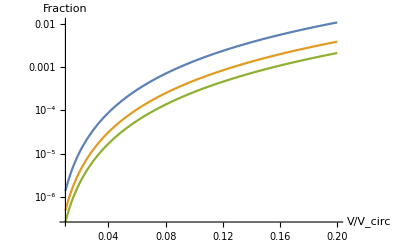

```mathematica
Fs=Fv[x,#]&/@{0,1,√2};
LogPlot[Fs,{x,1*^-2,0.2},PlotRange->All,AxesLabel->{"V/V_circ", "Fraction"}]
```

Mass growth can be approximated with
1/(M_(bh,i))-1/(M_(bh,f))~ ∫Gρ/V_rel^3 dt=∫Gρ/V_rel^3 dx/V_bh
We know probability distribution of V_rel, V_bh and ρ,
P(log ρ) ~ N(-σ_ρ^2/2, σ_ρ)

Naively, we assume that there is only one dense clump in the whole medium. At radius r from the center of the density peak, the density is ρ_c, then the mean density insider the sphere is
ρ̄=(∫_ρ_c)^∞P(ρ)ρ dρ/(∫_ρ_c)^∞P(ρ)dρ
The mass inside the sphere is
M_clump=M_cl(∫_ρ_c)^∞P(ρ)ρ dρ/(∫_0)^∞P(ρ)ρ dρ=M_cl/ρ_0×(∫_ρ_c)^∞P(ρ)ρ dρ
Then the radius is about
r~ (M_clump/(ρ̄))^(1/3) ~ ((4π)/3)^(1/3)R_0[(∫_ρ_c)^∞P(ρ)dρ]^(1/3)=((2π)/3)^(1/3)R_0[1-erf((log (ρ_c/ρ_0)+σ_ρ^2/2)/(√2 σ_ρ))]^(1/3)
The volume swept by the sphere is π r^2 V T, let V ~ √(G M_cl/R) and T=α_t t_(ff,0), the possibility of encountering a BH is
F_ρ~π r^2 α_t R/(4π R^3/3)=(3 α_t)/4(((2π)/3)^(1/3)[1-erf((log (ρ_c/ρ_0)+σ_ρ^2/2)/(√2 σ_ρ))])^(1/3)

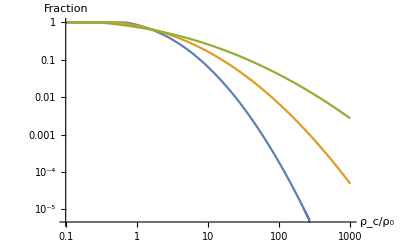

```mathematica
Fρ[y_,σ_,αt_]:=Min[1,(3αt)/4((2π)/3)^(1/3)(1-Erf[(Log [y]+σ^2/2)/(√2 σ)])^(1/3)];
Fs=Fρ[x,#,1]&/@{1/√2,1,√2};
LogLogPlot[Fs,{x,.1,1000},PlotRange->All,AxesLabel->{"ρ_c/ρ_0", "Fraction"}]
```

We need to consider the relation between ρ_c and the average density ρ̄.

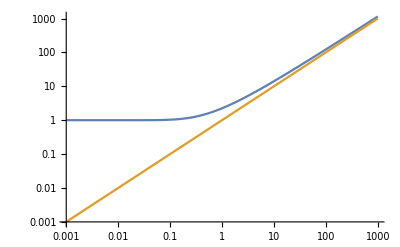

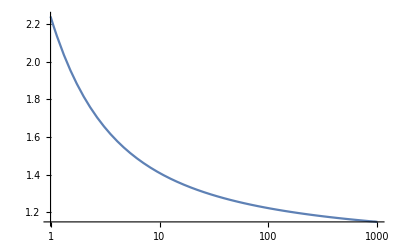

```mathematica
ρcl[y_,σ_]:=(1-Erf[(Log [y]-σ^2/2)/(√2 σ)])/(1-Erf[(Log [y]+σ^2/2)/(√2 σ)])
LogLogPlot[{ρcl[x,1],x},{x,1*^-3,1*^3}]
LogLinearPlot[{ρcl[x,1]/x},{x,1,1*^3}]
```

Though the two quantities are different, they asymptotically converge at high density. Since we only care about high densities, we try to ignore the difference here.

From what we know, 
1/(M_(bh,i))-1/(M_(bh,f))=γ/M_cl,
γ=((ρ̄)/ρ_0)^(1/2)(V/V_circ)^-3.
Thus for γ, the CDF is determined by
P_γ(Z<γ)=∫p_ρ(y)(∫_(γ^(-1/3)y^(1/6)))^∞ p_v(x) dx dy=(∫_0)^∞p_ρ(y)(1-P_v(y^(1/6)/γ^(1/3)))dy

```mathematica
(*Fρ[y_,σ_,αt_]:=(1/2-1/2*Erf[(Log [y])/(√2 σ)])^(1/3)*)
```

```mathematica
Fγ[z_,σρ_]:=NIntegrate[-D[Fρ[y,σρ,1],y]*(1-Fv[y^(1/6)/z^(1/3),1]),{y,1*^-6,1000.}]
```

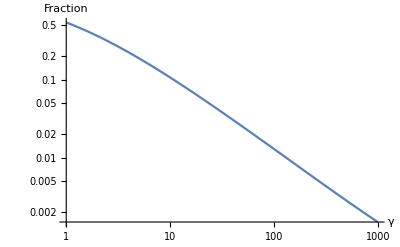

```mathematica
LogLogPlot[1-Fγ[x],{x,1,1000},PlotRange->All,AxesLabel->{"γ","Fraction"}]
```

```mathematica
Fγ[z_,σρ_:2,αv_:0.5]:=NIntegrate[D[Fv[x,αv],x]*(1-Fρ[z^2 x^-6,σρ,1]),{x,1*^-6,1*^6}]
```

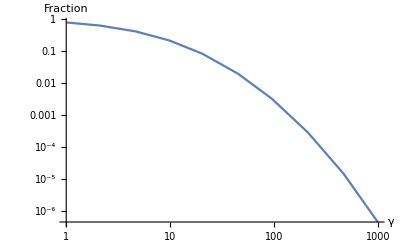

```mathematica
LogLogPlot[1-Fγ[x],{x,1,1*^3},PlotRange->All,AxesLabel->{"γ","Fraction"},PlotPoints->10,MaxRecursion->0]
```

The accreted mass is
ΔM_bh/M_bh=γM_bh/(M_cl-γM_bh).
Assuming that the mass ratio is r=M_bh/M_cl, then the CDF of ΔM_bh/M_bh for r=0.001,0.01,0.1 is

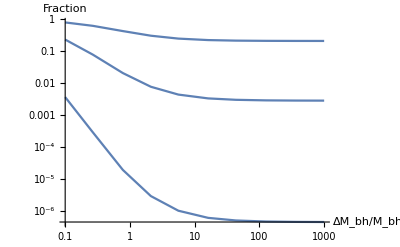

```mathematica
LogLogPlot[Table[1-Fγ[x/(rr*(x+1))],{rr,{0.001,0.01,0.1}}],{x,.1,1000},PlotRange->All,AxesLabel->{"ΔM_bh/M_bh", "Fraction"},PlotPoints->10,MaxRecursion->0]
```

So far the basic assumptions are: the velocity dispersion of gas and BHs are the same; the density log-normal distribution has σ=1.

Assuming that the initial mass of the cloud is 10^8 M_sun, for a BH with initial mass of 10^4 M_sun, CDF of the final mass is

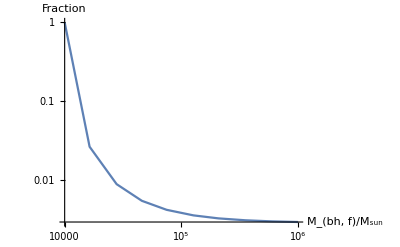

```mathematica
mtot=1*^6;
mbh=1*^4;
rr=mbh/mtot;
LogLogPlot[1-Fγ[(x-mbh)/(rr*x)],{x,mbh,mbh*100},PlotRange->All,AxesLabel->{"M_(bh, f)/M_sun", "Fraction"},PlotPoints->10,MaxRecursion->0]
```

```mathematica
Fbh[x_,mbh_,mtot_]:=Fγ[(x-mbh)/(mbh/mtot*x)];
ml=1*^2;
mh=1*^4;
Fbhall[x_]:=NIntegrate[,{y,ml,mh}]
```